# Figure 2: GPS Breeding w/ Post Selection

## Set-Up

Define parameter space.

```mathematica
nSpace = DeleteCases[DeleteCases[Range[7,40],37],39];
GKPSqdB = Range[0.01,12,0.05];
```

Retrieve the GPS breeding output states (GPSBreedingOutputStates), the optimal squeezing to use for damping (DampingSqdBTable), the optimal GKP qubit squeezing to compare damped states to (TargetGKPSq), and homodyne distribution integration limits (PHomIntLims).

```mathematica
Get["Figure 2/GPSBreedingOutputStates"];
Get["Figure 2/DampingSqdBTable"];
Get["Figure 2/TargetGKPSq"];
Get["Figure 2/PHomIntLims"];
```

The homodyne probability distribution associated with the GPS breeding output state φnp is Pnp.

```mathematica
f[n_,k_]:= Exp[-1/2*2 *Pi/n*pTilde^2]*Sum[(-1)^l*Binomial[n,k]*Binomial[2*k,2*l]*((4*Pi^2*pTilde^2)/n^2)^(k-l)*((4*Pi)/n)^(l+1/2)*Gamma[l+1/2],{l,0,2*k}];
Pnp[n_]:=(1/Gamma[n+1/2]*(n/(4*Pi))^n*Sqrt[n]/(2*Pi))^2*Sum[f[n,k]*f[n,kPrime]*((2*Pi)/n)^(2*n-k-kPrime+1/2)*Gamma[2*n-k-kPrime+1/2],{kPrime,0,n},{k,0,n}];
```

The GPS success probabiity, with max probability input squeezing  (r_max) and number of photons detected (n) is given by PGPS.

```mathematica
PGPS[n_]:=(2^-n n^n (1+2 n)^(-1/2-n) Gamma[1+2 n])/(n!)^2;
```

## Target States

Generating logical 0 qubit GKP wavefunctions taking into account m = 0th, 1st, and ∞ peaks

```mathematica
(*IdealGKP0 = ParallelTable[{GKPSqdB[[ii]],(Exp[-1/2 Exp[-2*r]*(2*0*Sqrt[Pi])^2]*Exp[-1/2*((x-2*0(Sqrt[Pi]))/Exp[-r])^2])/Sqrt[NIntegrate[(Exp[-1/2 Exp[-2*r]*(2*0*Sqrt[Pi])^2]*Exp[-1/2*((x-2*0(Sqrt[Pi]))/Exp[-r])^2])^2/.r->Log[10^(GKPSqdB[[ii]]/10)]/2,{x,-∞,∞}]]/.r->Log[10^(GKPSqdB[[ii]]/10)]/2},{ii,1,Length[GKPSqdB]}];
IdealGKP1 = ParallelTable[{GKPSqdB[[ii]],(Sum[Exp[-1/2 Exp[-2*r]*(2*t*Sqrt[Pi])^2]*Exp[-1/2*((x-2*t(Sqrt[Pi]))/Exp[-r])^2],{t,-1,1}])/Sqrt[NIntegrate[(Sum[Exp[-1/2 Exp[-2*r]*(2*t*Sqrt[Pi])^2]*Exp[-1/2*((x-2*t(Sqrt[Pi]))/Exp[-r])^2],{t,-1,1}])^2/.r->Log[10^(GKPSqdB[[ii]]/10)]/2,{x,-∞,∞}]]/.r->Log[10^(GKPSqdB[[ii]]/10)]/2},{ii,1,Length[GKPSqdB]}];
IdealGKPInf = ParallelTable[{GKPSqdB[[ii]],(Sum[Exp[-1/2 Exp[-2*r]*(2*t*Sqrt[Pi])^2]*Exp[-1/2*((x-2*t(Sqrt[Pi]))/Exp[-r])^2],{t,-10,10}])/Sqrt[NIntegrate[(Sum[Exp[-1/2 Exp[-2*r]*(2*t*Sqrt[Pi])^2]*Exp[-1/2*((x-2*t(Sqrt[Pi]))/Exp[-r])^2],{t,-10,10}])^2/.r->Log[10^(GKPSqdB[[ii]]/10)]/2,{x,-∞,∞}]]/.r->Log[10^(GKPSqdB[[ii]]/10)]/2},{ii,1,Length[GKPSqdB]}];*)
```

```mathematica
Get["Figure 2/IdealGKP0"];
Get["Figure 2/IdealGKP1"];
Get["Figure 2/IdealGKPInf"];
```

## Apply Damping Operation

The damping operation is done by applying QND interaction (U = ⅇ^-ix1p2) to input state and a squeezed state and detecting zero photons in second mode. P(Damp) is the the normalization constant of the heralded state

```mathematica
UnNormalizedDampedStates =Table[{nSpace[[ii]],DampingSqdBTable[[ii,2]],If[DampingSqdBTable[[ii,2]]==Infinity,GPSBreedingOutputStates[[ii,2]], GPSBreedingOutputStates[[ii,2]]*ⅇ^(1/4 x^2 (-1+Tanh[r])) √Sech[r]/.{r->Log[10^(DampingSqdBTable[[ii,2]]/10)]/2}]},{ii,1,Length[nSpace]}];
ProbDamp = ParallelTable[{nSpace[[ii]],If[DampingSqdBTable[[ii,2]]==Infinity,1,NIntegrate[UnNormalizedDampedStates[[ii,3]]*UnNormalizedDampedStates[[ii,3]],{x,-∞,∞}]]},{ii,1,Length[nSpace]}];
NormalizedDampedStates = Table[{nSpace[[ii]],DampingSqdBTable[[ii,2]], If[DampingSqdBTable[[ii,2]]==Infinity,GPSBreedingOutputStates[[ii,2]],UnNormalizedDampedStates[[ii,3]]/Sqrt[ProbDamp[[ii,2]]]]},{ii,1,Length[nSpace]}];
```

## Fidelity Calculation

Calculate the fidelity between the optimal output states and target GKP qubits.

```mathematica
(*FidelityIntegrandTable = Table[{nSpace[[ii]],NormalizedDampedStates[[ii,3]]*IdealGKPInf[[Position[GKPSqdB,TargetGKPSq[[ii,2]]][[1,1]],2]]},{ii,1,Length[nSpace]}];FidTable =ParallelTable[{nSpace[[ii]],Abs[NIntegrate[FidelityIntegrandTable[[ii,2]],{x,-∞,∞}]]^2},{ii,1,Length[nSpace]}];*)
Get["Figure 2/FidTable"];
```

## Success Probability Calculations

The total probability of the scheme is P = (P(GPS_Max))^2 * P(Hom)*P(Damp). We define P(GPS_Max) to be the GPS success probability when the input states have squeezing such that of detecting n photons is maximized, P(Hom) is the homodyne measurement success probability, and  P(Damp) is the success probability of the damping operation.

We calculated the homodyne success probability by integrating Pnp over the finite acceptance widows. (Note the factors of 2 are due to the symmetry of Pnp about the origin)

```mathematica
(*HomSuccessProb=ParallelTable[If[OddQ[nSpace[[ii]]]==False,Total[{NIntegrate[PTildenp[nSpace[[ii]]],{pTilde,PHomIntLims[[ii,2,1,1]],PHomIntLims[[ii,2,1,2]]}],2*NIntegrate[PTildenp[nSpace[[ii]]],{pTilde,PHomIntLims[[ii,2,2,1]],PHomIntLims[[ii,2,2,2]]}],2*NIntegrate[PTildenp[nSpace[[ii]]],{pTilde,PHomIntLims[[ii,2,3,1]],PHomIntLims[[ii,2,3,2]]}]}],Total[{2*NIntegrate[PTildenp[nSpace[[ii]]],{pTilde,PHomIntLims[[ii,2,1,1]],PHomIntLims[[ii,2,1,2]]}],2*NIntegrate[PTildenp[nSpace[[ii]]],{pTilde,PHomIntLims[[ii,2,2,1]],PHomIntLims[[ii,2,2,2]]}]}]],{ii,1,Length[nSpace]}];*)
Get["Figure 2/HomSuccessProb"];
```

Calculating total success probability

```mathematica
TotalProb = Table[PGPS[nSpace[[ii]]]^2*HomSuccessProb[[ii]]*ProbDamp[[ii,2]],{ii,1,Length[nSpace]}];
TotalProb//ScientificForm
```

{1.28618×10^-4,6.77762×10^-5,6.78974×10^-5,5.01567×10^-5,3.97802×10^-5,3.34959×10^-5,2.74198×10^-5,2.29832×10^-5,2.04392×10^-5,1.62623×10^-5,1.48761×10^-5,1.18079×10^-5,1.08602×10^-5,8.55363×10^-6,8.10461×10^-6,6.98178×10^-6,6.09076×10^-6,5.30407×10^-6,4.45407×10^-6,3.84015×10^-6,1.3946×10^-5,1.35321×10^-5,1.20203×10^-5,1.17079×10^-5,1.04243×10^-5,1.02554×10^-5,9.08661×10^-6,9.07538×10^-6,8.00561×10^-6,8.06757×10^-6,7.2×10^-6,6.44767×10^-6}

## P_(no error) Calculations

Calculate the P_(no error) for damped output states.

```mathematica
(*OutputStateNoErrorP = ParallelTable[{{TargetGKPSq[[ii,2]],1/Sqrt[Pi]*Sum[Quiet[NIntegrate[Exp[2*I*v*Sqrt[Pi]*(s-t)](NormalizedDampedStates[[ii,3]]/.{x->2*s*Sqrt[Pi]+u})*(NormalizedDampedStates[[ii,3]]/.{x->2*t*Sqrt[Pi]+u}),{u,-Sqrt[Pi]/6,Sqrt[Pi]/6},{v,-Sqrt[Pi]/6,Sqrt[Pi]/6},Method->"Trapezoidal"]],{t,-10,10},{s,-10,10}]}},{ii,1,Length[nSpace]}];*)
Get["Figure 2/OutputStateNoErrorP"];
```

Calculate the P_(no error) for target GKP qubits with m = 0th, 1st, and ∞ peaks .

```mathematica
(*IdealGKPNoErrorPm0 = ParallelTable[{GKPSqdB[[ii]],1/Sqrt[Pi]*NIntegrate[(IdealGKP0[[ii,2]]/.{x->2*0*Sqrt[Pi]+u})*(IdealGKP0[[ii,2]]/.{x->2*0*Sqrt[Pi]+u}),{u,-Sqrt[Pi]/6,Sqrt[Pi]/6},{v,-Sqrt[Pi]/6,Sqrt[Pi]/6},Method->"Trapezoidal"]},{ii,1,Length[GKPSqdB]}];
IdealGKPNoErrorPm1 = ParallelTable[{GKPSqdB[[ii]],1/Sqrt[Pi]*Sum[NIntegrate[Exp[2*I*v*Sqrt[Pi]*(s-t)](IdealGKP1[[ii,2]]/.{x->2*s*Sqrt[Pi]+u})*(IdealGKP1[[ii,2]]/.{x->2*t*Sqrt[Pi]+u}),{u,-Sqrt[Pi]/6,Sqrt[Pi]/6},{v,-Sqrt[Pi]/6,Sqrt[Pi]/6}],{t,-1,1},{s,-1,1}]},{ii,1,Length[GKPSqdB]}];
IdealGKPNoErrorPmInf = ParallelTable[{GKPSqdB[[ii]],1/Sqrt[Pi]*Sum[Quiet[NIntegrate[Exp[2*I*v*Sqrt[Pi]*(s-t)](IdealGKPInf[[ii,2]]/.{x->2*s*Sqrt[Pi]+u})*(IdealGKPInf[[ii,2]]/.{x->2*t*Sqrt[Pi]+u}),{u,-Sqrt[Pi]/6,Sqrt[Pi]/6},{v,-Sqrt[Pi]/6,Sqrt[Pi]/6},Method->"Trapezoidal"]],{t,-10,10},{s,-10,10}]},{ii,1,Length[GKPSqdB]}];*)
Get["Figure 2/IdealGKPNoErrorPm0"];
Get["Figure 2/IdealGKPNoErrorPm1"];
Get["Figure 2/IdealGKPNoErrorPmInf"];
```

## Plots

Plot fidelity .

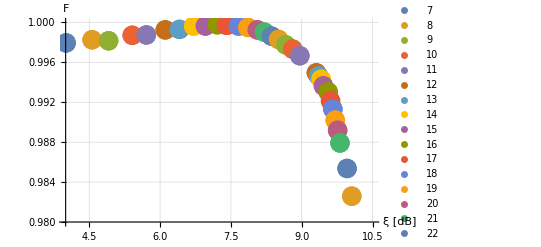

```mathematica
PlotFidvsGKPSq= Table[{{TargetGKPSq[[ii,2]],FidTable[[ii,2]]}},{ii,1,Length[nSpace]}];
FidPlot= ListPlot[PlotFidvsGKPSq,PlotMarkers->{"●",Large},PlotRange->{{4,10.5},{0.98,1.}},AxesLabel->{Style["ξ [dB]",Large, Black],Style["F",Large, Black]},TicksStyle->Directive[ 24],PlotLegends->Table[ToString[nSpace[[ii]]],{ii,1,Length[nSpace]}],GridLines->Automatic];
Show[FidPlot]
```

Plot success probability .

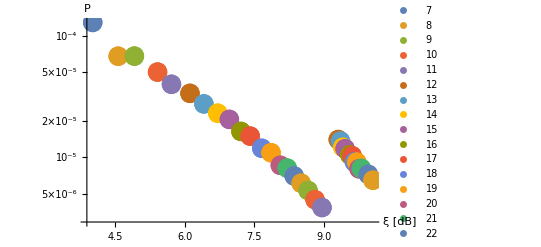

```mathematica
PlotTotalProbvsGKPSq = Table[{{TargetGKPSq[[ii,2]],TotalProb[[ii]]}},{ii,1,Length[nSpace]}];
SuccessProbPlot= ListLogPlot[PlotTotalProbvsGKPSq,PlotMarkers->{"●",Large},PlotRange->All,AxesLabel->{Style["ξ [dB]",Large, Black],Style["P",Large, Black]},TicksStyle->Directive[24],GridLines->Automatic,PlotLegends->Table[ToString[nSpace[[ii]]],{ii,1,Length[nSpace]}]];
Show[SuccessProbPlot]
```

Plot the P_(no error) for output state and target GKP qubits with m = 0th, 1st, and ∞ peaks .

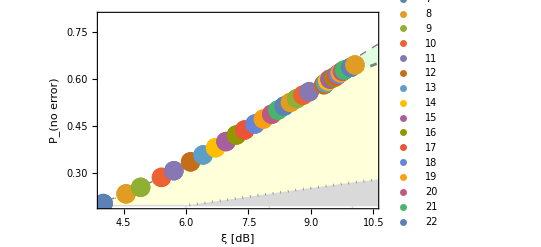

```mathematica
NoErrorPlot0 = Graphics[ListLinePlot[{{0,0.2},{11.959,0.2}},PlotRange->{{4,10.5},{0.2,0.8}},Filling->{1->{15,LightGray}},PlotStyle->{LightGray}],GridLines->{{4,6,8,10,12}, {0.2,0.4,0.6,0.8}}];
NoErrorPlot1 = Graphics[ListLinePlot[IdealGKPNoErrorPm0,PlotRange->{{4,10.5},{0.2,0.8}},PlotStyle->{Gray,Dotted},Filling->{1->{15,LightYellow}}],GridLines->{{4,6,8,10,12}, {0.2,0.4,0.6,0.8}},Method->{"FrameInFront",True},Frame->True];
NoErrorPlot2 = Graphics[ListLinePlot[IdealGKPNoErrorPm1,PlotRange->{{4,10.5},{0.2,0.8}},PlotStyle->{Gray,DotDashed},Filling->{1->{15,LightGreen}}],GridLines->{{4,6,8,10,12}, {0.2,0.4,0.6,0.8}},Method->{"AxesInFront",True}];
NoErrorPlot3 = Graphics[ListLinePlot[IdealGKPNoErrorPmInf,PlotRange->{{4,10.5},{0.2,0.8}},PlotStyle->{Gray,Dashed,Thick},Filling->{1->{15,White}}],GridLines->{{4,6,8,10,12}, {0.2,0.4,0.6,0.8}},Method->{"GridLinesInFront"->True},TicksStyle->Directive[24]];
NoErrorPlot4=ListPlot[ OutputStateNoErrorP,PlotMarkers->{"●",Large},PlotRange->{{4,10.5},{0.2,0.8}},PlotStyle->{PointSize[0.025]},PlotLegends->Table[ToString[nSpace[[ii]]],{ii,1,Length[nSpace]}]];
Show[NoErrorPlot0,NoErrorPlot1,NoErrorPlot2,NoErrorPlot3,NoErrorPlot4,Frame->True,FrameTicksStyle->Large ,GridLines->{{4,6,8,10,12}, {0.2,0.3,0.4,0.5,0.6,0.7,0.8}},Method->{"GridLinesInFront"->True},GridLinesStyle->Directive[LightGray,Thickness[0.0025]],FrameLabel->{Style["ξ [dB]",Large, Black],Style["P_(no error)",Large, Black]}]
```